```mathematica
k[β_,z_]:=
k[β,z]=z^(β/2)Hypergeometric2F1[β/2,β/2,β,z];

(*Conformal Blocks in 2D CFT*)
g[Δ_,L_][z_,zb_]:=k[Δ+L,z]k[Δ-L,zb]+k[Δ-L,z]k[Δ+L,zb];

(*Crossing Function*)
F[Δϕ_,Δ_,L_][z_,zb_]:=((((1-z)(1-zb))^(Δϕ))*g[Δ,L][z,zb]-((z*zb)^(Δϕ))*g[Δ,L][1-z,1-zb])/(((z*zb)^(Δϕ))-(((1-z)(1-zb))^(Δϕ)));

(*2D Vector Map*)
vector[f_]:={f[0.5,0.6]-f[0.5,0.333],f[0.5,0.6]-f[0.333,0.25]};
```

```mathematica
(*This is a function that normalises a vector, so that we get all values in a range*)
normalisedVector[Δϕ_,Δ_,L_]:=Module[{
v=vector[F[Δϕ,Δ,L]],
λ=If[L>0,1-L/20,1-(Δ-L)/10]
},(λ*v)/Norm[v]
];

nicePlotOptions={PlotRange->{{-1,1},{-1,1}},
AspectRatio->1,Joined->True,
InterpolationOrder->4
};
```

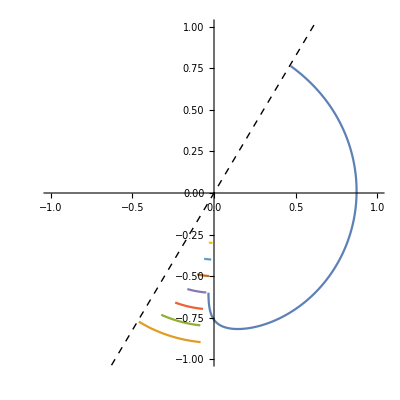

```mathematica
(*Constructing the Spin-l Operators*)
Module[{
Δϕ=0.125,
τmin=0.01,
τmax=4,
Lmax=14,
stressTensorVector,
blockVectors,
ΔscalarMin=1.04
},
stressTensorVector=normalisedVector[Δϕ,2,2];
blockVectors=Table[normalisedVector[Δϕ,Δ,L],
{L,0,Lmax,2},{Δ,If[L==0,ΔscalarMin,L+τmin],L+τmax,If[L==0,1/400,1/10]}];
Show[
ListPlot[
blockVectors,
nicePlotOptions
],
Graphics[
{Dashed,Line[{2*stressTensorVector,-2*stressTensorVector}]}
]
]
]
```